```mathematica
{g,h10,h20}={9.8,2,1}    ;
Eqn1 =v[t]- Sqrt[2*g*(h1[t]-h2[t])]==0    ;
h1[t]=h10-(v[t]*t)/50  ;
h2[t]=h20+(v[t]*t)/50    ;
sol1=Solve[Eqn1,v[t]];
sol1[[2,1,2]]

Solve[sol1[[2,1,2]]==0,t]
```

9.43709×10^-17 (-4.15382×10^15 t+√(2.2008×10^33+1.72542×10^31 t^2))

{{t→0.+5.19308×10^8 ⅈ}}

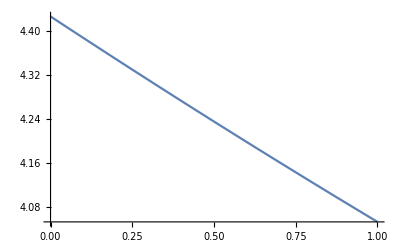

```mathematica
Plot[sol1[[2,1,2]],{t,0,1}]
```